```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

styles={Directive[RGBColor[0,0,0],AbsoluteThickness[3.5]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,1],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[2],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[2],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};

(*FrameTicksFontSize=16;
FrameFontSize=16;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->0.75,ImageSize->Medium,PlotStyle->styles,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];*)

Nf=3;
eg=16Pi^2/30;
eq=6*3*7Pi^2/120;  (*check these later*)
sFac = eg+eq ;

rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->2000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];
```

```mathematica
(*** e(T), P(T) lattice data ***)

eosDataRaw2=Import[wd<>"/best.dat"];
energy= eosDataRaw2[[1;;450,6]];
pressure=eosDataRaw2[[1;;450,3]];
entropy=eosDataRaw2[[1;;450,4]];
temp = 0.005067731*eosDataRaw2[[1;;450,2]];  (* convert units to fm^-1 *)

temp[[2]]-temp[[1]];

pressureTdata=Table[{temp[[i]],pressure[[i]]},{i,1,Length[pressure]}];
energyTdata=Table[{temp[[i]],energy[[i]]},{i,1,Length[energy]}];
entropyTdata=Table[{temp[[i]],entropy[[i]]},{i,1,Length[entropy]}];

edInt=Interpolation[energyTdata];
PInt=Interpolation[pressureTdata];
SInt=Interpolation[entropyTdata];

temp[[450]];
0.499*5.067731;
edInt[temp[[450]]]
edInt[.155*5.067721]
PInt[temp[[440]]];
SInt[temp[[440]]]
(edInt[temp[[440]]]+PInt[temp[[440]]])/temp[[440]]
```

525.751

1.81842

254.076

254.089

523.599

523.599

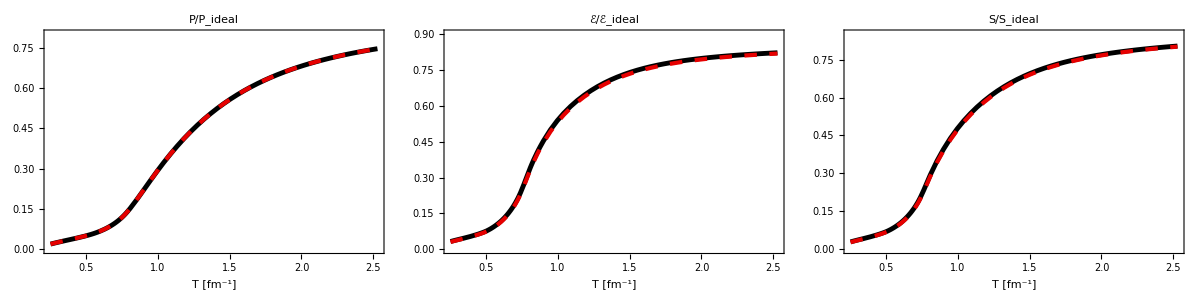

```mathematica
Tmin = temp[[1]];
Tmax=temp[[450]];

Pfit[T_]=PInt[T];

Sfit[T_]=Pfit'[T];

efit[T_]=T*Sfit[T]-Pfit[T];

emin=efit[Tmin];
emax=efit[Tmax];
523.5987775189976

emax

Grid[{{Plot[{PInt[T]/(sFac T^4/3),Pfit[T]/(sFac T^4/3)},{T,Tmin,Tmax},PlotRange->{0,0.8},PlotStyle->styles,PlotLabel->Style["P/P_ideal",FontSize->20],ImageSize->320,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{edInt[T]/(sFac T^4),efit[T]/(sFac T^4)},{T,Tmin,Tmax},PlotRange->{0,0.9},PlotStyle->styles,PlotLabel->Style["ℰ/ℰ_ideal",FontSize->20],ImageSize->320,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{SInt[T]/(4.0/3.0*sFac T^3),Sfit[T]/(4.0/3.0*sFac T^3)},{T,Tmin,Tmax},PlotRange->{0,0.85},PlotStyle->styles,PlotLabel->Style["S/S_ideal",FontSize->20],ImageSize->320,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

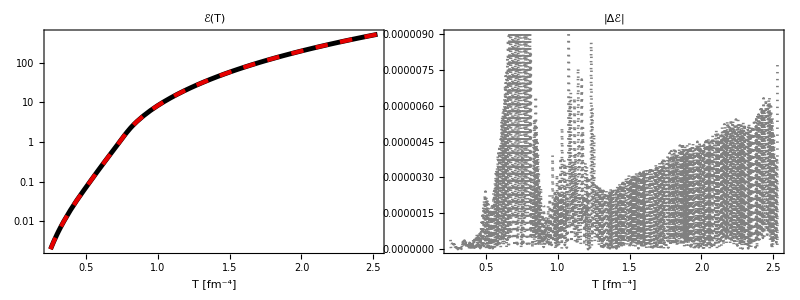

(-0.002999930312462119 + 0.09417646213801027*T - 1.3472144415370244*Power(T,2) + 11.531744338662536*Power(T,3) - 
     65.17050664643754*Power(T,4) + 252.96623410554895*Power(T,5) - 673.9895236411604*Power(T,6) + 
     1155.6029102124326*Power(T,7) - 910.3488025995453*Power(T,8) - 971.3230107937379*Power(T,9) + 
     3724.9276204901016*Power(T,10) - 4118.540210991578*Power(T,11) - 78.52429756414836*Power(T,12) + 
     5293.81004825622*Power(T,13) - 4557.553823074766*Power(T,14) - 3240.888013850884*Power(T,15) + 
     10697.194999962052*Power(T,16) - 11211.426603636184*Power(T,17) + 6481.455655216752*Power(T,18) - 
     2082.163818010678*Power(T,19) + 293.70151601812523*Power(T,20))/
   (0.607428913591128 - 9.953288454061427*T + 73.64572871160192*Power(T,2) - 322.3694142746391*Power(T,3) + 
     912.7288538270155*Power(T,4) - 1687.858513517085*Power(T,5) + 1840.856145562391*Power(T,6) - 
     470.3775809532542*Power(T,7) - 1924.6292185965883*Power(T,8) + 3047.9613287381467*Power(T,9) - 
     1074.1083334677714*Power(T,10) - 2852.0884246377973*Power(T,11) + 5597.783660696195*Power(T,12) - 
     5456.527953543836*Power(T,13) + 3464.3092713525684*Power(T,14) - 1521.9174635327095*Power(T,15) + 
     471.31297621425625*Power(T,16) - 104.13673393295115*Power(T,17) + 16.227425444403956*Power(T,18) - 
     1.5313653054600316*Power(T,19) + 0.0661997114240791*Power(T,20))

```mathematica
(*** e(T) ***)

efitdata=Table[{temp[[i]],efit[temp[[i]]]},{i,1,Length[temp]}];

n =20;

efitfit[T_]=rationalPolyFit[efitdata,n,n]/.{x->T};

Grid[{{
LogPlot[{efit[T],efitfit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["ℰ(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{Abs[efit[T]-efitfit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|Δℰ|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
CForm[efitfit[T]]
```

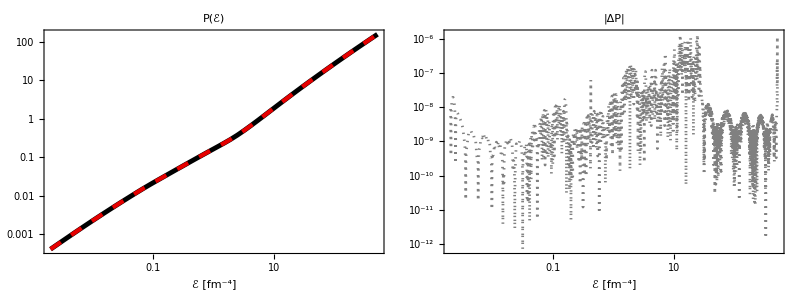

(7.190009839568977e-11 - 1.395774723345131e-6*e - 0.0007294542973192687*Power(e,2) - 0.02755303080259852*Power(e,3) + 
     0.6777139269471448*Power(e,4) - 2.5676157307802105*Power(e,5) - 198.27861304635795*Power(e,6) + 
     2892.771435243516*Power(e,7) - 20443.08028356625*Power(e,8) + 26431.269835104275*Power(e,9) + 
     54554.71732475857*Power(e,10) - 136384.84011985105*Power(e,11) + 170729.28261000666*Power(e,12) - 
     109354.23042660154*Power(e,13) + 47809.54395258853*Power(e,14) - 10743.012809422258*Power(e,15) + 
     1573.4464820882827*Power(e,16) + 73.09843404933184*Power(e,17) + 33.75839022332086*Power(e,18) + 
     22.370532570822895*Power(e,19) + 0.8661540343959165*Power(e,20) + 0.00823546974656238*Power(e,21) + 
     0.000011977402417543487*Power(e,22) - 3.823554294234436e-8*Power(e,23) - 4.015185097090365e-11*Power(e,24))/
   (-7.4539090540790035e-6 - 0.003091276650747094*e - 0.10715341272046117*Power(e,2) + 
     2.2410756562049117*Power(e,3) + 3.147397633194132*Power(e,4) - 977.4165681862902*Power(e,5) + 
     12218.017097992242*Power(e,6) - 74668.39069402599*Power(e,7) - 8194.662719386062*Power(e,8) + 
     604927.8696703409*Power(e,9) - 1.1027507974839194e6*Power(e,10) + 1.2140822058208985e6*Power(e,11) - 
     738923.1898118919*Power(e,12) + 316237.5914113029*Power(e,13) - 71392.6962417791*Power(e,14) + 
     11335.190090043036*Power(e,15) - 109.3640028588883*Power(e,16) + 449.6151741523075*Power(e,17) + 
     106.96820874330709*Power(e,18) + 3.348031043873812*Power(e,19) + 0.027585414077599367*Power(e,20) + 
     0.0000337469979928549*Power(e,21) - 1.252632993005512e-7*Power(e,22) - 1.2345479534532178e-10*Power(e,23) + 
     1.2680975061416364e-16*Power(e,24))

```mathematica
(*** P(e) ***)

PdataED=Table[{efit[temp[[i]]],Pfit[temp[[i]]]},{i,1,Length[temp]}];
Pfunc=Interpolation[PdataED];

n =24;

PfitED[e_]=rationalPolyFit[PdataED,n,n]/.{x->e};

Grid[{{
LogLogPlot[{Pfunc[e],PfitED[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["P(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLogPlot[{Abs[Pfunc[e]-PfitED[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|ΔP|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
CForm[PfitED[e]]
```

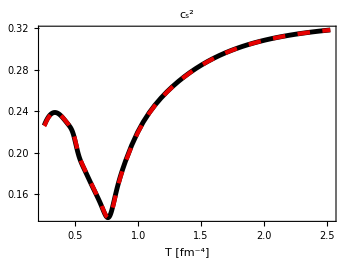

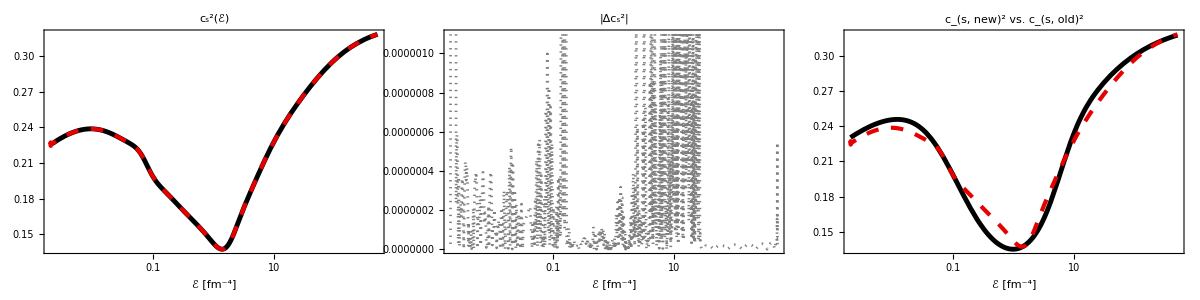

(-8.313077825923736e-14 - 9.91131461236627e-11*e + 4.9370463998042573e-8*Power(e,2) + 
     0.000012403698595004402*Power(e,3) - 0.0006912983927137311*Power(e,4) + 0.021581851285318674*Power(e,5) - 
     0.3403540349639598*Power(e,6) + 2.571364021486668*Power(e,7) + 6.673093766060017*Power(e,8) - 
     243.3375964116734*Power(e,9) + 1814.6643869387997*Power(e,10) - 2548.2582086974326*Power(e,11) + 
     2765.630246068556*Power(e,12) - 1875.00259667093*Power(e,13) + 1108.2896957487499*Power(e,14) - 
     404.3458694331876*Power(e,15) + 102.97057964895681*Power(e,16) - 8.666160558180495*Power(e,17) + 
     1.7034256926427882*Power(e,18) + 0.1509835583259864*Power(e,19) + 0.0022131911506897946*Power(e,20) - 
     2.1845675724304455e-6*Power(e,21) - 4.963727093415996e-9*Power(e,22))/
   (-4.616396862584361e-13 - 3.6987626554837435e-10*e + 2.2199967297197156e-7*Power(e,2) + 
     0.00004628916421708627*Power(e,3) - 0.002304008118798134*Power(e,4) + 0.06298983609139512*Power(e,5) - 
     0.6406277787382678*Power(e,6) - 3.5167650188178268*Power(e,7) + 192.24184427400343*Power(e,8) - 
     2117.4295381872043*Power(e,9) + 11548.342629589715*Power(e,10) - 13151.384905721165*Power(e,11) + 
     11212.491449000934*Power(e,12) - 4742.373401294556*Power(e,13) + 3067.8255158942507*Power(e,14) - 
     1331.2232187171192*Power(e,15) + 433.2239004538602*Power(e,16) - 32.73752014120429*Power(e,17) + 
     8.258268788269858*Power(e,18) + 0.5504745185457142*Power(e,19) + 0.006760130196823705*Power(e,20) - 
     7.032724563397889e-6*Power(e,21) - 1.513558086157459e-8*Power(e,22))

```mathematica
(*** Subscript[c, s]^2(e) ***)


(*Subscript[c, s]^2 = dp/de = dp/dT dT/de = s dT/de= (e+p)/(T de/dT)*)

cs2temp[T_]=(efit[T]+Pfit[T])/(T*efit'[T]);

cs2original[T_]=(edInt[T]+PInt[T])/(T*edInt'[T]);

Plot[{cs2original[T],cs2temp[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["c_s^2",FontSize->24],Axes->False,FrameLabel->{"T [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]

cs2data=Table[{efit[temp[[i]]],cs2temp[temp[[i]]]},{i,1,Length[temp]}];

cs2=Interpolation[cs2data];

n =22;

cs2fit[e_]=rationalPolyFit[cs2data,n,n]/.{x->e};

cs2old[e_]=(5.191934309650155*10^-32+4.123605749683891*10^-23*e+3.1955868410879504*10^-16*e^2+1.4170364808063119*10^-10*e^3+6.087136671592452*10^-6*e^4+0.02969737949090831*e^5+15.382615282179595*e^6+460.6487249985994*e^7+1612.4245252438795*e^8+275.0492627924299*e^9+58.60283714484669*e^10+6.504847576502024*e^11+0.03009027913262399*e^12+8.189430244031285*10^-6*e^13)/(1.4637868900982493*10^-30+6.716598285341542*10^-22*e+3.5477700458515908*10^-15*e^2+1.1225580509306008*10^-9*e^3+0.00003551782901018317*e^4+0.13653226327408863*e^5+60.85769171450653*e^6+1800.5461219450308*e^7+15190.225535036281*e^8+590.2572000057821*e^9+293.99144775704605*e^10+21.461303090563028*e^11+0.09301685073435291*e^12+0.000024810902623582917*e^13);

Grid[{{
LogLinearPlot[{cs2[e],cs2fit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["c_s^2(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLinearPlot[{Abs[cs2[e]-cs2fit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|Δc_s^2|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLinearPlot[{cs2old[e],cs2fit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["c_(s, new)^2 vs. c_(s, old)^2",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

CForm[cs2fit[e]]
```

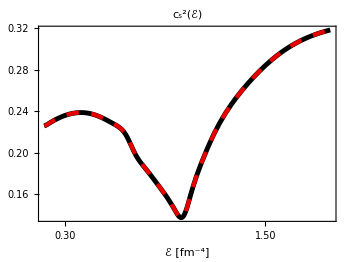

```mathematica
(** check chain rule in cs2 relations **)

LogLinearPlot[{cs2temp[T],cs2[efit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["c_s^2(ℰ)",FontSize->24],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

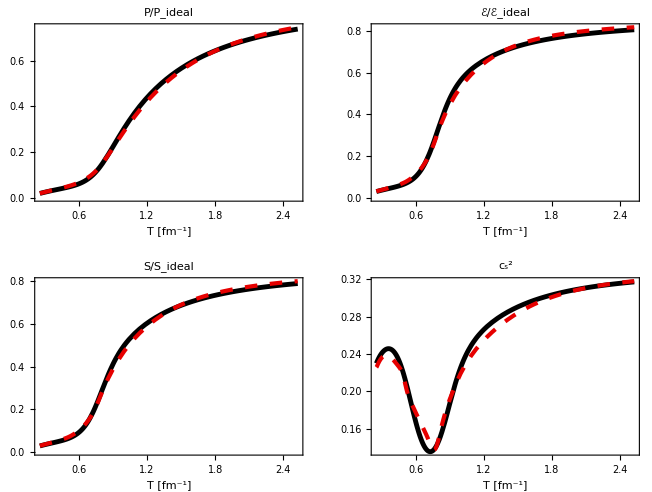

```mathematica
(*** Compare to old EOS data (black) ***)


eosDataRaw=Import[wd<>"/eos.dat"];
eosData= Take[eosDataRaw,{3,Length[eosDataRaw]}];
(* Subscript[ϵ, eq](T) *)
LogEDLogTInt = Interpolation[eosData[[All,{1,2}]]];
edIntold[T_] = 10^LogEDLogTInt[Log[10,T]];
(* Subscript[P, eq](T) *)
LogPLogTInt = Interpolation[eosData[[All,{1,4}]]];
PIntold[T_] = 10^LogPLogTInt[Log[10,T]];
(* Subscript[c, s]^2(T) *)
LogdPLogEdInt = Interpolation[eosData[[All,{2,5}]]];
dPIntE[e_]=10^LogdPLogEdInt[Log[10,e]];
LogdELogEdInt = Interpolation[eosData[[All,{2,3}]]];
dEIntE[e_]=10^LogdELogEdInt[Log[10,e]];
cs2Int[T_] = dPIntE[edIntold[T]]/dEIntE[edIntold[T]];

GraphicsGrid[{{Plot[{PIntold[T]/(sFac T^4/3),Pfit[T]/(sFac T^4/3)},{T,Tmin,Tmax},PlotStyle->styles,PlotLabel->Style["P/P_ideal",FontSize->24],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{edIntold[T]/(sFac T^4),efit[T]/(sFac T^4)},{T,Tmin,Tmax},PlotStyle->styles,PlotLabel->Style["ℰ/ℰ_ideal",FontSize->24],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]},
{Plot[{(edIntold[T]+PIntold[T])/(4.0/3.0*sFac T^4),(Sfit[T])/(4.0/3.0*sFac T^3)},{T,Tmin,Tmax},PlotStyle->styles,PlotLabel->Style["S/S_ideal",FontSize->24],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{cs2Int[T],cs2temp[T]},{T,Tmin,Tmax},PlotStyle->styles,PlotLabel->Style["c_s^2",FontSize->24],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]
```

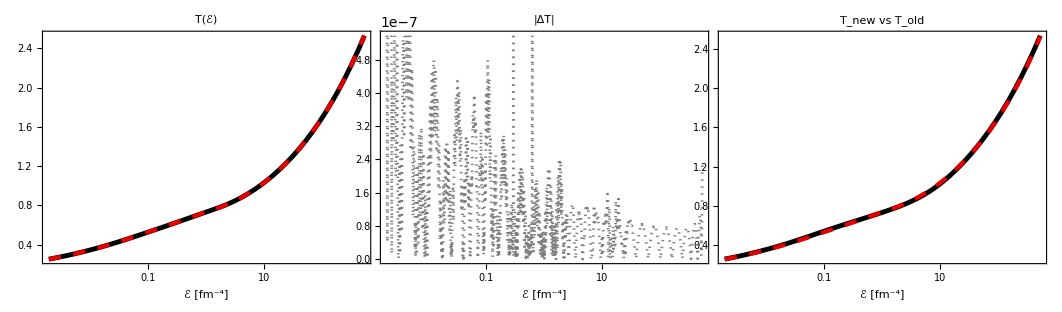

(6.354702650133721e-7 + 0.0016261450306068567*e + 0.45825931456340785*Power(e,2) + 14.188693412528751*Power(e,3) - 
     314.7885041652167*Power(e,4) + 2378.640132157695*Power(e,5) + 25273.133749493598*Power(e,6) - 
     140224.9709264792*Power(e,7) + 106293.04579291707*Power(e,8) + 89517.1975351415*Power(e,9) - 
     70843.79668025293*Power(e,10) + 28526.039709340683*Power(e,11) - 36943.18834114948*Power(e,12) + 
     189251.03702063803*Power(e,13) - 51967.87699872343*Power(e,14) + 7691.785198380105*Power(e,15) + 
     9513.282503693723*Power(e,16) + 482.55672261331955*Power(e,17) + 5.389198283394992*Power(e,18) + 
     0.013817918026243032*Power(e,19) + 5.570450207372526e-6*Power(e,20))/
   (4.1560932681286e-6 + 0.006747031242574442*e + 1.285101644232421*Power(e,2) + 19.36905363832382*Power(e,3) - 
     639.5077730169339*Power(e,4) + 7119.547834859753*Power(e,5) + 22354.06915581833*Power(e,6) - 
     197845.8735584382*Power(e,7) + 189101.14796407992*Power(e,8) + 117736.90044970746*Power(e,9) - 
     193723.6698826523*Power(e,10) + 186595.1710000764*Power(e,11) - 158312.42292489434*Power(e,12) + 
     320049.3255747058*Power(e,13) - 111686.06861346996*Power(e,14) + 25750.640860019877*Power(e,15) + 
     9437.496426864122*Power(e,16) + 334.06415213565924*Power(e,17) + 2.6440125443979445*Power(e,18) + 
     0.004563233640606438*Power(e,19) + 9.788656932810127e-7*Power(e,20))

```mathematica
(*** T(e) ***)

efit[0.155*5.067731];

TdataED=Table[{efit[temp[[i]]],temp[[i]]},{i,1,Length[temp]}];

Tfunc=Interpolation[TdataED];

n =20;

Tfit[e_]=rationalPolyFit[TdataED,n,n]/.{x->e};

Told[e_]=(2.059151308901543*10^-66+1.2883117551723254*10^-37*e+9.653685304732326*10^-18*e^2+0.0021387548523685764*e^3+3.152348276671561*10^7*e^4+6.128861811040275*10^14*e^5+1.2611913502159628*10^20*e^6+8.510311640702168*10^23*e^7+3.3406440917885196*10^26*e^8+9.526824863039937*10^27*e^9-5.540454604707275*10^27*e^10-3.834326779020863*10^28*e^11+2.732286036998176*10^28*e^12+3.389763887380034*10^27*e^13+3.271304177799644*10^25*e^14+3.5796316255209677*10^22*e^15+3.647754101481452*10^18*e^16)/(3.465150960288193*10^-64+7.292333136125966*10^-36*e+3.167120708990754*10^-16*e^2+0.047875501682141906*e^3+5.1924910033740276*10^8*e^4+7.186120863411006*10^15*e^5+9.741960860767537*10^20*e^6+3.9749426686364564*10^24*e^7+9.163047659503782*10^26*e^8+1.4902973847933083*10^28*e^9-1.710867316101183*10^28*e^10-4.366544624555957*10^28*e^11+3.801696016710178*10^28*e^12+2.43514662137169*10^27*e^13+1.376570820431094*10^25*e^14+8.761759990161081*10^21*e^15+4.265493796252328*10^17*e^16);

GraphicsGrid[{{
LogLinearPlot[{Tfunc[e],Tfit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->400,Frame->True,PlotLabel->Style["T(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],

LogLinearPlot[{Abs[Tfunc[e]-Tfit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->400,Frame->True,PlotLabel->Style["|ΔT|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],

LogLinearPlot[{Told[e],Tfit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->400,Frame->True,PlotLabel->Style["T_new vs T_old",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}},Spacings->{-50,0}]

CForm[Tfit[e]]
```

1.38708

1.38708

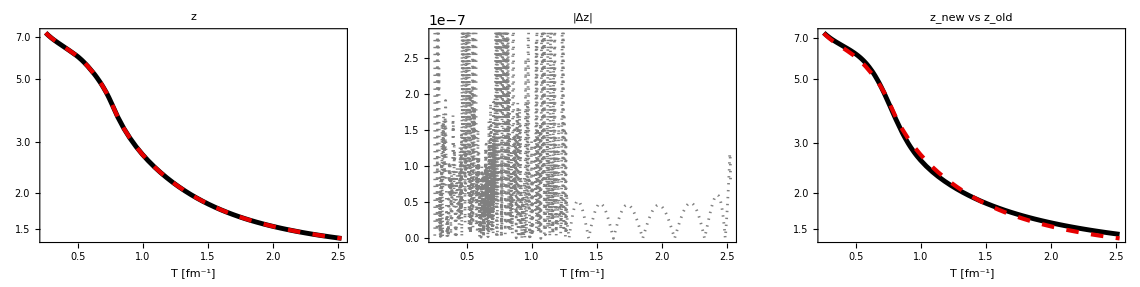

(-0.024849858891137756 + 0.47847736373416083*T - 4.61918347715829*Power(T,2) + 29.068429322455216*Power(T,3) - 
     124.71500934989882*Power(T,4) + 351.97333774650616*Power(T,5) - 574.5614209565085*Power(T,6) + 
     242.47052067855995*Power(T,7) + 939.3631556394441*Power(T,8) - 1497.7161122587*Power(T,9) - 
     869.1541853013247*Power(T,10) + 4463.510513169322*Power(T,11) - 3155.388775545533*Power(T,12) - 
     3669.9148634996404*Power(T,13) + 6025.055619284398*Power(T,14) + 2530.010229436638*Power(T,15) - 
     12377.828009524466*Power(T,16) + 11064.662640234146*Power(T,17) - 1367.8202341736014*Power(T,18) - 
     5153.441529030352*Power(T,19) + 4692.66519828337*Power(T,20) - 1839.6486572686679*Power(T,21) + 
     295.61128212686765*Power(T,22))/
   (-0.0013353616408144687 + 0.01630070964709733*T - 0.0940784693091734*Power(T,2) + 0.39761014119292426*Power(T,3) - 
     1.0902179925763675*Power(T,4) - 0.6350707349088213*Power(T,5) + 17.49970782818318*Power(T,6) - 
     54.253564043787605*Power(T,7) + 31.303530751694325*Power(T,8) + 188.09655216728908*Power(T,9) - 
     410.4192207829322*Power(T,10) - 46.729398612517514*Power(T,11) + 1123.465391973284*Power(T,12) - 
     861.0382656839028*Power(T,13) - 2009.5894022610644*Power(T,14) + 4034.061184550695*Power(T,15) + 
     82.58158725655181*Power(T,16) - 9138.895740558035*Power(T,17) + 15147.595016391986*Power(T,18) - 
     13280.168404822247*Power(T,19) + 7035.328067245568*Power(T,20) - 2154.9632787206424*Power(T,21) + 
     297.54649144190483*Power(T,22))

```mathematica
(*** z(T) ***)

nc = 3.0;
nf = 3.0;
g =Pi^4/180.0*(4.0*(nc^2-1.0)+7.0*nc*nf);
F[T_]=(2.0*Pi^2)/g*Sfit[T]/T^3;

zQuasi=Table[{temp[[i]],""},{i,1,Length[temp]}];

zQuasi[[Length[zQuasi],2]]=x/.FindRoot[x^3*BesselK[3,x]==F[temp[[450]]],{x,1.3},MaxIterations->5000]

For[i = Length[zQuasi]-1, i >0,i--,
zQuasi[[i,2]]=x/.FindRoot[x^3*BesselK[3,x]==F[zQuasi[[i,1]]],{x,zQuasi[[i+1,2]]},MaxIterations->5000];
]

zQuasifunc=Interpolation[zQuasi];

zQuasidata=Table[{T,zQuasifunc[T]},{T,Tmin,Tmax, 0.005067731}];

n = 22;

zQuasifit[T_]=rationalPolyFit[zQuasidata,n,n]/.{x->T};

zQuasifit[temp[[450]]]


zold[T_]=(2.195527549421445*10^-14+5.014273212142939*10^-11*T+6.8769768080936324*10^-9*T^2-1.3090323372462384*10^-6*T^3+0.00007503723419734601*T^4-0.0019335423100477788*T^5+0.0077581370622797526*T^6+1.0840238709953247*T^7-40.41237726417249*T^8+815.5709414412947*T^9-11117.3113417968*T^10+107720.35990943392*T^11-727161.0603316505*T^12+3.12288627176472*10^6*T^13-7.240727201149486*10^6*T^14+8.813651470346985*10^6*T^15-3.535759885234317*10^6*T^16-5.454281769326236*10^6*T^17+1.0415987187648855*10^7*T^18-8.0189396235499745*10^6*T^19+2.6430627991581215*10^6*T^20)/(1.1541703277540495*10^-16+4.122377967105372*10^-13*T+1.2528690762234088*10^-10*T^2-1.1203883703791743*10^-8*T^3-3.65428489042621*10^-8*T^4+0.00004068369176438496*T^5-0.0024580222716044254*T^6+0.08433957015198745*T^7-2.0279246693088906*T^8+36.56366190486074*T^9-490.05025567116945*T^10+4477.3308927313055*T^11-21467.525530376926*T^12-23929.310531648207*T^13+889228.088912891*T^14-4.262596231414713*10^6*T^15+1.0642287968093066*10^7*T^16-1.643826578603126*10^7*T^17+1.6160269998993594*10^7*T^18-9.40765741315934*10^6*T^19+2.502796051035953*10^6*T^20);

GraphicsGrid[{{
LogPlot[{zQuasifunc[T],zQuasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["z",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{Abs[zQuasifunc[T]-zQuasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δz|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogPlot[{zold[T],zQuasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["z_new vs z_old",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

zQuasifit[T]//CForm
```

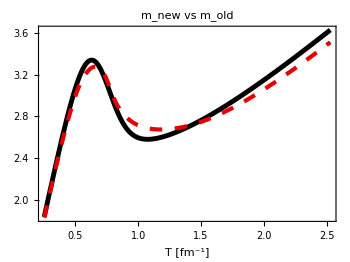

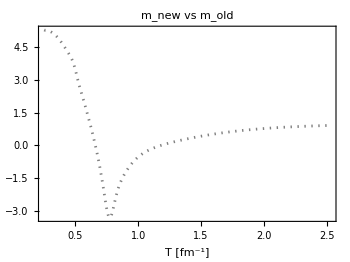

```mathematica
mQuasifunc[T_] =T*zQuasifunc[T]; 

Plot[{T*zold[T],mQuasifunc[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["m_new vs m_old",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]

Plot[{mQuasifunc'[T]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["m_new vs m_old",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

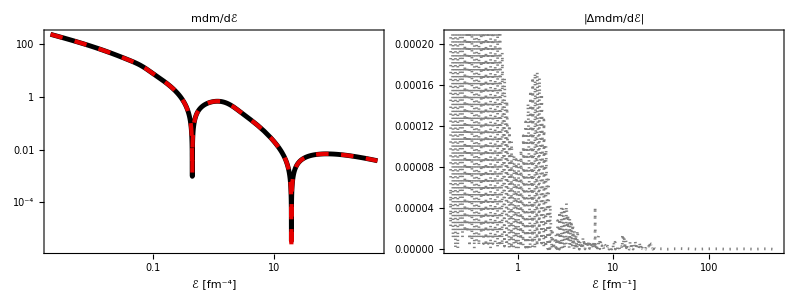

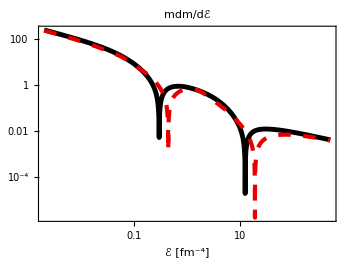

(-1.1927967184213977e-16 - 6.93974002078785e-14*e + 1.9869461829302351e-10*Power(e,2) - 
     8.208591908642511e-8*Power(e,3) + 2.1583246622414057e-6*Power(e,4) + 0.00295868687991236*Power(e,5) - 
     0.17822845705127216*Power(e,6) + 5.475450243005113*Power(e,7) - 112.74127105299743*Power(e,8) + 
     1792.0308572672911*Power(e,9) - 23579.344765116297*Power(e,10) + 255189.75987280835*Power(e,11) - 
     2.150714313919863e6*Power(e,12) + 1.3217785117761483e7*Power(e,13) - 5.577544865333324e7*Power(e,14) + 
     1.5312086360101765e8*Power(e,15) - 2.6254487591150045e8*Power(e,16) + 2.8330538234837854e8*Power(e,17) - 
     2.0088099636636007e8*Power(e,18) + 8.347774051502697e7*Power(e,19) - 2.0059418552083727e7*Power(e,20) + 
     2.3761027880381965e6*Power(e,21) - 177245.14183632794*Power(e,22) + 14339.985029833542*Power(e,23) - 
     425.93472333750054*Power(e,24) - 2.577223524643679*Power(e,25) - 0.0008855556603909956*Power(e,26))/
   (3.0182841741089683e-21 - 6.577567640649949e-16*e + 4.815941355358405e-13*Power(e,2) + 
     9.975024228049674e-11*Power(e,3) - 1.3894925021353866e-7*Power(e,4) + 0.000022993194037377313*Power(e,5) + 
     0.0012773521621841865*Power(e,6) - 0.1065579618826654*Power(e,7) + 3.590371338387996*Power(e,8) - 
     80.48923667947855*Power(e,9) + 1393.5544507541963*Power(e,10) - 18894.187421954797*Power(e,11) + 
     192969.21573898598*Power(e,12) - 1.408144757359425e6*Power(e,13) + 6.7921946177834235e6*Power(e,14) - 
     1.8712911902045455e7*Power(e,15) + 1.804160400553675e7*Power(e,16) + 2.8706083779758964e7*Power(e,17) - 
     6.826894176947126e7*Power(e,18) + 6.86350446212044e7*Power(e,19) - 3.355884995662966e7*Power(e,20) + 
     9.82011720923614e6*Power(e,21) - 1.659176852926879e6*Power(e,22) + 322524.77250394184*Power(e,23) - 
     29476.7992154663*Power(e,24) - 486.03870527880787*Power(e,25) - 0.8934224937867911*Power(e,26))

```mathematica
(*** m(e) and dm/de ***) 

mdataED=Table[{efit[temp[[i]]],temp[[i]]*zQuasifunc[temp[[i]]]},{i,1,Length[temp]}];

mfunc=Interpolation[mdataED];

mdmde[e_]=mfunc[e]*mfunc'[e];

mdmdedata=Table[{efit[temp[[i]]],mdmde[efit[temp[[i]]]]},{i,1,Length[temp]}];

n =26;

mdmdefit[e_]=rationalPolyFit[mdmdedata,n,n]/.{x->e};

mdmdeold[e_]=(1.0932938963420931*10^-38-1.007252920091783*10^-31*e+1.258073500377669*10^-25*e^2+3.7902939287037426*10^-19*e^3+9.982754875153906*10^-14*e^4+5.356830067926448*10^-9*e^5+0.00006631556444292836*e^6+0.19429591145238154*e^7+133.14135704995198*e^8+19906.496386848434*e^9+468502.08289765124*e^10-2.1057407552865325*10^6*e^11-3.1682608543291925*10^6*e^12+1.7046132756833293*10^7*e^13-1.3636657914477058*10^7*e^14+2.0863251242849804*10^7*e^15-2.0496583087455064*10^7*e^16-4.069098068002096*10^7*e^17+3.445677209399048*10^7*e^18-3.7295352481362685*10^6*e^19+212848.6045508894*e^20-15965.651067054185*e^21+532.5403558600549*e^22+2.411729540242231*e^23+0.00027216645617684197*e^24)/(1.8097473184974786*10^-43-1.1919700038034044*10^-36*e-2.880545193459095*10^-30*e^2+1.5774335161251585*10^-23*e^3+1.2056411612584795*10^-17*e^4+1.5859303052883873*10^-12*e^5+4.642427449619644*10^-8*e^6+0.0003211322658208788*e^7+0.5307842016671973*e^8+205.22641687449376*e^9+17197.020001063076*e^10+262076.7134892617*e^11+1.517168279215402*10^6*e^12-4.41387607180566*10^6*e^13-4.689689648983293*10^6*e^14-1.1727564734279385*10^6*e^15+4.517859607565268*10^6*e^16+1.8472203478591543*10^7*e^17+1.8233835956962608*10^7*e^18-2.052678068458237*10^7*e^19+1.7590273805695719*10^6*e^20-448178.89154244727*e^21+13727.684912668212*e^22+572.3076682226775*e^23+0.5135708549693685*e^24);


Grid[{{LogLogPlot[{Abs[mdmde[e]],Abs[mdmdefit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLinearPlot[{Abs[mdmde[e]-mdmdefit[e]]},{e,100emin,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δmdm/dℰ|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

LogLogPlot[{Abs[mdmdeold[e]],Abs[mdmdefit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]

mdmdefit[e]//CForm
```

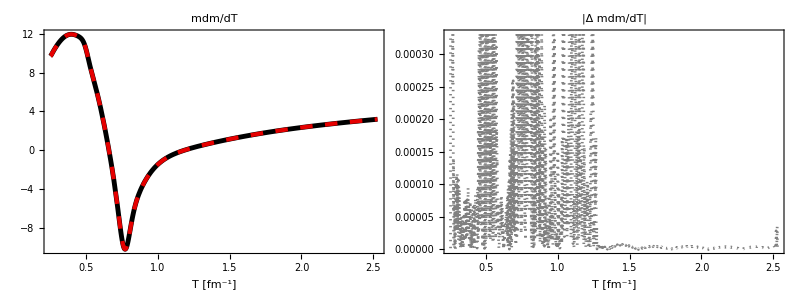

(0.005608417560932825 - 0.15965291363321024*T + 2.146506769835765*Power(T,2) - 17.354276998247887*Power(T,3) + 
     90.32274484030113*Power(T,4) - 303.9265552567468*Power(T,5) + 618.9905393945672*Power(T,6) - 
     547.5562832445656*Power(T,7) - 521.9462027835724*Power(T,8) + 1721.3151516515818*Power(T,9) - 
     731.2096347868167*Power(T,10) - 1443.9401042636614*Power(T,11) - 870.4569183528523*Power(T,12) + 
     6551.503232236555*Power(T,13) - 2627.2113280358517*Power(T,14) - 12604.448964689245*Power(T,15) + 
     14332.100188698501*Power(T,16) + 15118.33682963929*Power(T,17) - 53173.87779136548*Power(T,18) + 
     64976.55134638874*Power(T,19) - 47204.94046858447*Power(T,20) + 22377.742131747196*Power(T,21) - 
     6920.108193943858*Power(T,22) + 1288.320465405942*Power(T,23) - 110.20189027654786*Power(T,24))/
   (0.0009776516320639935 - 0.027168677980705117*T + 0.36163512058041053*Power(T,2) - 2.9924085159293328*Power(T,3) + 
     16.698862761287625*Power(T,4) - 64.11109829416328*Power(T,5) + 165.27786952094266*Power(T,6) - 
     255.31075747680555*Power(T,7) + 111.74686388172418*Power(T,8) + 408.3025042325941*Power(T,9) - 
     816.3191564786562*Power(T,10) + 158.2107422849028*Power(T,11) + 1375.9994607373835*Power(T,12) - 
     1655.0619808217239*Power(T,13) - 646.2615866628834*Power(T,14) + 3079.1521065329284*Power(T,15) - 
     2128.8975162162155*Power(T,16) - 1555.3566029797023*Power(T,17) + 3997.0020859286547*Power(T,18) - 
     3369.047525396329*Power(T,19) + 1418.9666183145537*Power(T,20) - 165.7711875848563*Power(T,21) - 
     124.81414498920952*Power(T,22) + 61.01936402944954*Power(T,23) - 8.765538990619126*Power(T,24))

```mathematica
(*** m dm/dT ***) 

mQuasifunc[T_] =T*zQuasifunc[T]; 

mdmdTQuasi[T_] = mQuasifunc[T] *D[ mQuasifunc[T],T];

(*mdmdTQuasi[T_] = mQuasifunc[T]*(zQuasifunc[T]+T*zQuasifunc'[T]);*)

mdmdTQuasidata=Table[{temp[[i]],mdmdTQuasi[temp[[i]]]},{i,1,Length[temp]}];

n = 24;

mdmdTQuasifit[T_]=rationalPolyFit[mdmdTQuasidata,n,n]/.{x->T};
Grid[{{
Plot[{mdmdTQuasi[T],mdmdTQuasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["mdm/dT",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[mdmdTQuasi[T]-mdmdTQuasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δ mdm/dT|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

mdmdTQuasifit[T]//CForm
```

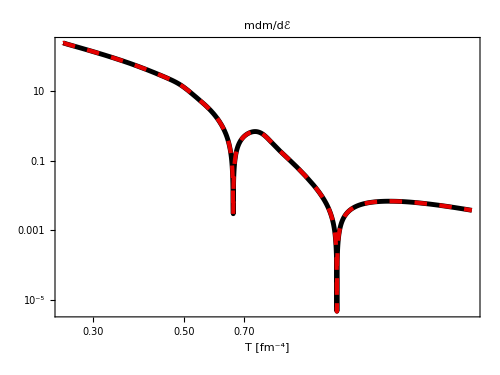

```mathematica
(*** check chain rule in relation: dm/de = cs2/s dm/dT ***)

LogLogPlot[{Abs[mdmdefit[efit[T]]],Abs[cs2fit[efit[T]]/Sfit[T]*mdmdTQuasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->500,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->24],Axes->False,FrameLabel->{"T [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

-11.5777

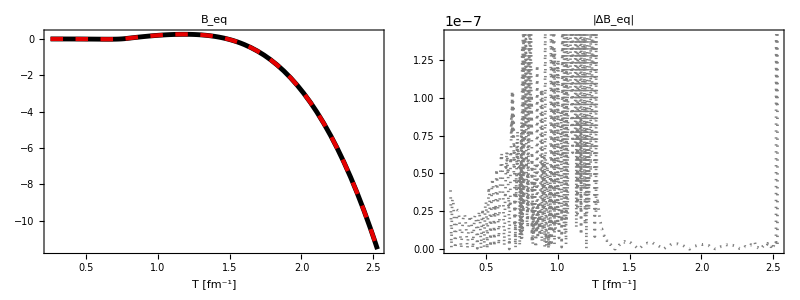

(0.050807553593981314 - 1.5689532639107107*T + 22.058925282111556*Power(T,2) - 186.46436942623802*Power(T,3) + 
     1054.8363701384187*Power(T,4) - 4208.039545493059*Power(T,5) + 12118.826371672492*Power(T,6) - 
     25136.8737959246*Power(T,7) + 35854.55231319769*Power(T,8) - 28711.571443848883*Power(T,9) - 
     6069.162219288527*Power(T,10) + 53559.81412173025*Power(T,11) - 78331.6574712575*Power(T,12) + 
     58756.1396988773*Power(T,13) - 12443.794232270604*Power(T,14) - 23027.5229322638*Power(T,15) + 
     29559.10660409062*Power(T,16) - 18193.57166869241*Power(T,17) + 6630.21829352344*Power(T,18) - 
     1368.9464729972105*Power(T,19) + 123.57849591412831*Power(T,20))/
   (54.333991663395125 - 892.1598816769438*T + 6678.706492335427*Power(T,2) - 30133.53859399463*Power(T,3) + 
     91127.7739984867*Power(T,4) - 193659.35059973205*Power(T,5) + 292541.0089980787*Power(T,6) - 
     303878.2121603155*Power(T,7) + 183600.71746461073*Power(T,8) + 7590.438830781842*Power(T,9) - 
     150077.88979897177*Power(T,10) + 178076.66061809257*Power(T,11) - 123525.97200512807*Power(T,12) + 
     56749.22929795278*Power(T,13) - 16975.405747105848*Power(T,14) + 2887.6602368384947*Power(T,15) - 
     135.07044953188364*Power(T,16) - 33.34448249826969*Power(T,17) + 4.918440361610946*Power(T,18) - 
     0.4806683822803251*Power(T,19) + 0.02067796139693879*Power(T,20))

```mathematica
(*** Subscript[B, eq](T) alternative ***)

n = 20;
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]];

B0Quasi2=Table[{temp[[i]],Pquasi[temp[[i]]]-Pfit[temp[[i]]]},{i,1,Length[temp]}];

B0Quasifunc2=Interpolation[B0Quasi2];

B0Quasifit2[T_]=rationalPolyFit[B0Quasi2,n,n]/.{x->T};

B0Quasifit2[temp[[450]]]

Grid[{{
Plot[{B0Quasifunc2[T],B0Quasifit2[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B_eq",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[B0Quasifunc2[T]-B0Quasifit2[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔB_eq|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

B0Quasifit2[T]//CForm

(* It's probably more accurate to calculate B this way *)
```

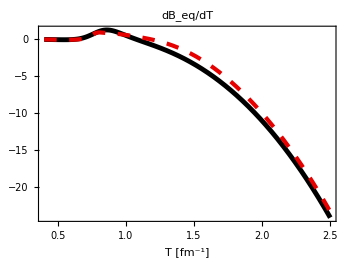

```mathematica
dmdTQuasi[T_]=mQuasifunc'[T];

mold[T_]=T*zold[T];

dmdTold[T_]=mold'[T];

H[T_] = -(g*T*mQuasifunc[T]*BesselK[1,zQuasifit[T]]*mdmdTQuasi[T])/(2.0*Pi^2);


H2[T_]=D[Pquasi[T]-Pfit[T],T];

Hfuncold[T_]=-(g*T^3*zold[T]^2*BesselK[1,zold[T]]*dmdTold[T])/(2.0*Pi^2);

Plot[{Hfuncold[T],H[T]},{T,.4,0.99temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["dB_eq/dT",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

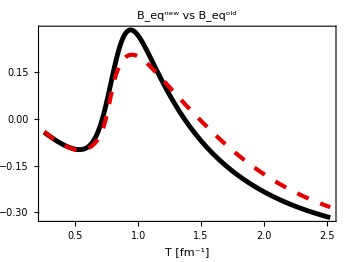

```mathematica
Beqold[T_]=(-0.003259287424704517+0.4709321130178677*T-18.471027719937705*T^2+334.0690722721871*T^3-3454.385244668648*T^4+22960.15979638924*T^5-105315.46668675772*T^6+346561.90522823617*T^7-836638.407629094*T^8+1.501743414016609*10^6*T^9-2.020237220416*10^6*T^10+2.0480693209160143*10^6*T^11-1.5779382837830463*10^6*T^12+943559.9448756306*T^13-456516.3985230772*T^14+185756.11302939596*T^15-61106.69072505601*T^16+13705.921942194844*T^17-1465.8180676090112*T^18)/(294.675932969415-1745.8088045773043*T+3997.025794070807*T^2-3586.7652790072334*T^3-1117.8588245192668*T^4+3765.9359654630407*T^5+841.4750390325167*T^6-4142.400568278239*T^7-1464.515167915579*T^8+4738.833500521431*T^9+2188.180519746309*T^10-6031.500378704362*T^11-203.76274436224986*T^12+5225.119313817963*T^13-3608.5761295285674*T^14+927.278254033823*T^15-80.77885500958108*T^16+4.197658993150538*T^17-0.10024694968615945*T^18);

Plot[{Beqold[T]/T^4,B0Quasifit2[T]/T^4},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B_eq^new vs B_eq^old",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

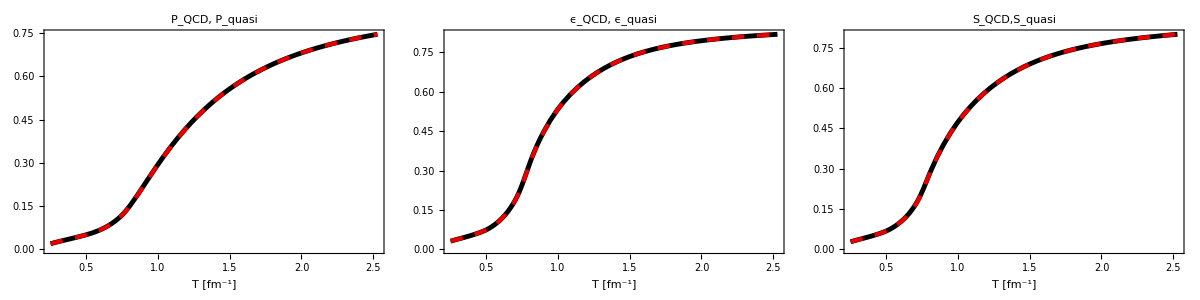

```mathematica
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]] -B0Quasifunc2[T];
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]])+B0Quasifunc2[T];

SQuasi[T_]=(Pquasi[T]+Equasi[T])/T;

Grid[{{Plot[{Pfit[T]/(sFac T^4/3),Pquasi[T]/(sFac T^4/3)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD, P_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{efit[T]/(sFac T^4),Equasi[T]/(sFac T^4)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD, ϵ_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Sfit[T]/(4*sFac*T^3/3),SQuasi[T]/(4*sFac*T^3/3)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"S_QCD,S_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

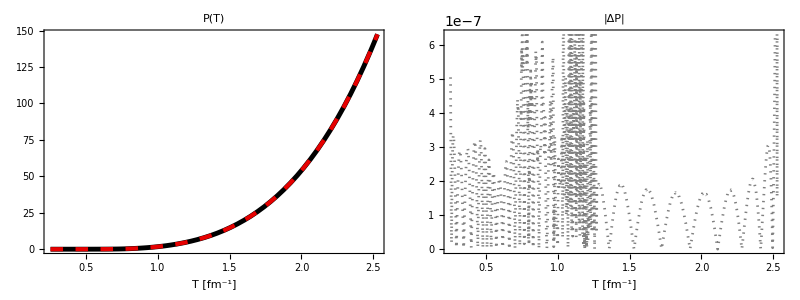

(0.00713009747608799 - 0.178239519999552*T + 2.018512591164485*Power(T,2) - 13.80079263600403*Power(T,3) + 
     64.18438030847095*Power(T,4) - 216.99055266437165*Power(T,5) + 557.7397322117549*Power(T,6) - 
     1129.1678142282658*Power(T,7) + 1849.9056915773876*Power(T,8) - 2478.8839032746123*Power(T,9) + 
     2673.5073156347235*Power(T,10) - 2214.1731000157533*Power(T,11) + 1301.3834717338107*Power(T,12) - 
     476.40578439958205*Power(T,13) + 80.87408873718634*Power(T,14))/
   (3.663492996566946 - 47.509051949201286*T + 279.83261064081745*Power(T,2) - 990.6348739721601*Power(T,3) + 
     2349.9851287659176*Power(T,4) - 3941.5415453542337*Power(T,5) + 4804.487048644571*Power(T,6) - 
     4304.437448115286*Power(T,7) + 2831.402877715671*Power(T,8) - 1351.9180865740618*Power(T,9) + 
     460.7826894778402*Power(T,10) - 111.05606505926326*Power(T,11) + 18.78241524013343*Power(T,12) - 
     1.9167366155553527*Power(T,13) + 0.08919008903949448*Power(T,14))

```mathematica
(* Fitting the quasiparticle kinetic pressure (B = 0) *)
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]];  (*kinetic only; no bag term*)
Pquasidata=Table[{temp[[i]],Pquasi[temp[[i]]]},{i,1,Length[temp]}];
n = 14;
Pquasifit[T_]=rationalPolyFit[Pquasidata,n,n]/.{x->T};

Grid[{{
Plot[{Pquasi[T],Pquasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["P(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[Pquasi[T]-Pquasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔP|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
Pquasifit[T]//CForm
```

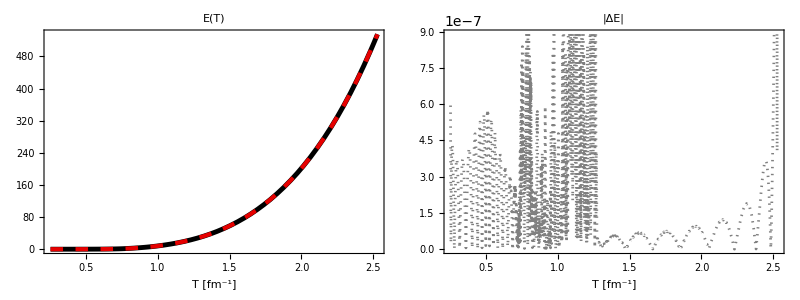

(-0.13036031705775997 + 3.802813405181376*T - 50.2025391664062*Power(T,2) + 395.1532253096646*Power(T,3) - 
     2053.6591855517413*Power(T,4) + 7351.206035098011*Power(T,5) - 18189.967920830615*Power(T,6) + 
     29667.196646109885*Power(T,7) - 25998.763198215744*Power(T,8) - 3679.044608449486*Power(T,9) + 
     35007.404309147496*Power(T,10) - 17841.369810679444*Power(T,11) - 49938.15692645847*Power(T,12) + 
     84482.68775270443*Power(T,13) - 10803.689520574771*Power(T,14) - 124330.63845728699*Power(T,15) + 
     201084.61833529465*Power(T,16) - 170532.72520194584*Power(T,17) + 88945.5433780969*Power(T,18) - 
     27385.907586083784*Power(T,19) + 3866.763131296266*Power(T,20))/
   (3.484913032612212 - 43.885045732165175*T + 245.46649123183352*Power(T,2) - 797.7936949667588*Power(T,3) + 
     1638.528852612137*Power(T,4) - 2093.6545050507198*Power(T,5) + 1264.864679373282*Power(T,6) + 
     747.1671173662737*Power(T,7) - 2039.8906141807045*Power(T,8) - 112.15619937823442*Power(T,9) + 
     6459.207792671554*Power(T,10) - 13655.811118485093*Power(T,11) + 16494.339704396978*Power(T,12) - 
     13217.140132893835*Power(T,13) + 7141.264431812377*Power(T,14) - 2499.30887010773*Power(T,15) + 
     527.4195201562281*Power(T,16) - 75.01629070456636*Power(T,17) + 14.492500648876549*Power(T,18) - 
     1.6482377983654652*Power(T,19) + 0.08348381592948188*Power(T,20))

```mathematica
(* Fitting the quasiparticle kinetic energy density (B = 0) *)
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]]);  (*kinetic only; no bag term*)
Equasidata=Table[{temp[[i]],Equasi[temp[[i]]]},{i,1,Length[temp]}];
n = 20;
Equasifit[T_]=rationalPolyFit[Equasidata,n,n]/.{x->T};
Grid[{{
Plot[{Equasi[T],Equasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["E(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[Equasi[T]-Equasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔE|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
Equasifit[T]//CForm
```

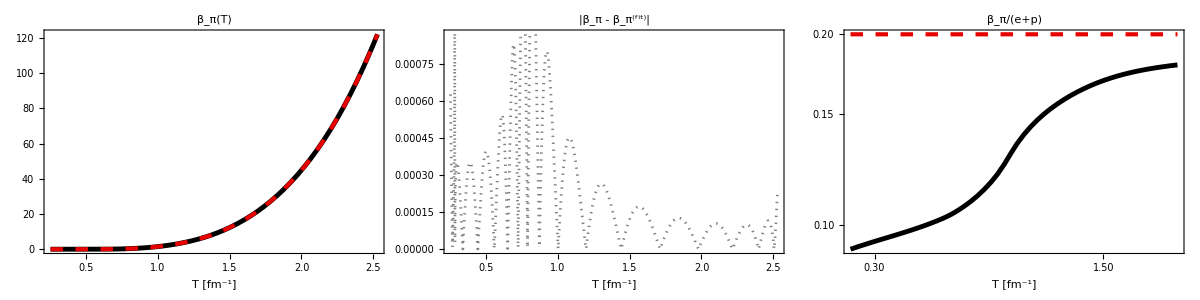

(-4.559186863959626 + 69.86334705250142*T - 425.07528354326666*Power(T,2) + 1268.059768668576*Power(T,3) - 
     1739.0260845778541*Power(T,4) + 356.80703482226835*Power(T,5) + 1303.8002405853554*Power(T,6) - 
     224.91212390972507*Power(T,7) - 900.6603057381708*Power(T,8) - 307.3985521264842*Power(T,9) + 
     303.35215554381773*Power(T,10) + 335.54179834641616*Power(T,11) + 99.6613576951631*Power(T,12) - 
     12.693372341662348*Power(T,13) + 24.77073181998932*Power(T,14))/
   (-15.35026621554268 + 48.7412789585087*T + 53.69554937572056*Power(T,2) - 84.82154942062445*Power(T,3) - 
     143.89514714218154*Power(T,4) + 29.92699172555165*Power(T,5) + 110.28001697309789*Power(T,6) + 
     60.71726923701555*Power(T,7) + 17.679870475805952*Power(T,8) + 15.107230793738804*Power(T,9) + 
     9.865144767539169*Power(T,10) - 1.4431339740643492*Power(T,11) - 2.060536863228295*Power(T,12) + 
     1.049091511320209*Power(T,13) - 0.1370012959279261*Power(T,14))

```mathematica
betapiDataRaw=Import[wd<>"/betapiplot.dat"];
betapiData= Take[betapiDataRaw,{2,Length[betapiDataRaw]}];
betapi = Interpolation[betapiData[[All,{1,2}]]];
n = 14;
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapiconformal[T_]=0.2*Sfit[T]*T;

Grid[{{Plot[{betapi[T],betapifit[T]},{T,temp[[1]],temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betapi[T]-betapifit[T]]},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_π - β_π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{betapi[T]/(T*Sfit[T]),betapiconformal[T]/(T*Sfit[T])},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
betapifit[T]//CForm
```

122.159

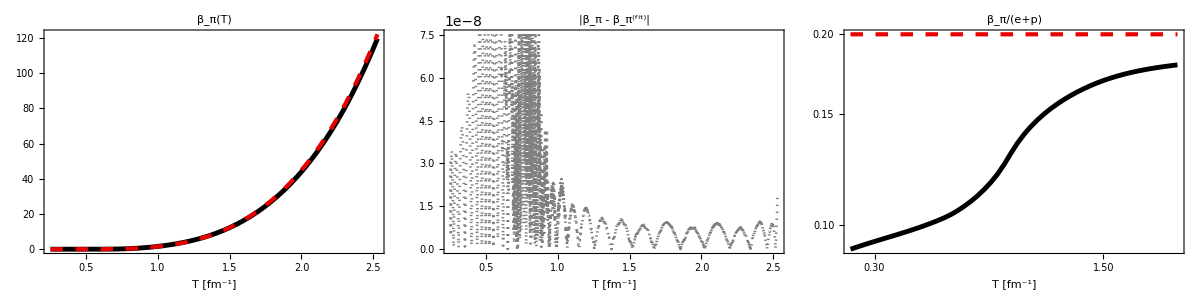

(-0.0006722334181861278 + 0.020981611799401487*T - 0.3003433271430471*Power(T,2) + 2.6116199518249665*Power(T,3) - 
     15.399829703103727*Power(T,4) + 65.06166059716692*Power(T,5) - 202.3666090447353*Power(T,6) + 
     466.25210726257365*Power(T,7) - 779.4904101385158*Power(T,8) + 868.8932139791635*Power(T,9) - 
     411.14645379600887*Power(T,10) - 592.667737068368*Power(T,11) + 1632.926083719566*Power(T,12) - 
     2069.890386136668*Power(T,13) + 1730.2242477404525*Power(T,14) - 1008.0678781446692*Power(T,15) + 
     400.90168230037744*Power(T,16) - 99.1842206133379*Power(T,17) + 11.623128893229937*Power(T,18))/
   (0.13545415941532687 - 1.7536013765581169*T + 9.969759116385646*Power(T,2) - 31.911955288131104*Power(T,3) + 
     58.81196007535421*Power(T,4) - 43.15017620990655*Power(T,5) - 78.55572516715633*Power(T,6) + 
     305.0037996396808*Power(T,7) - 529.5608501724396*Power(T,8) + 623.1858662882871*Power(T,9) - 
     551.3643680854686*Power(T,10) + 384.2132659431429*Power(T,11) - 214.54982845745045*Power(T,12) + 
     94.68381935636559*Power(T,13) - 31.389785266671918*Power(T,14) + 7.159273301573178*Power(T,15) - 
     1.0107938835056607*Power(T,16) + 0.08751702155436722*Power(T,17) - 0.003505831484556357*Power(T,18))

```mathematica
betapiDataRaw=Import[wd<>"/betapiplot.dat"];
betapiData= Take[betapiDataRaw,{2,Length[betapiDataRaw]}];
betapi = Interpolation[betapiData[[All,{1,2}]]];
n = 18;
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapiconformal[T_]=0.2*T*Sfit[T];

betapifit[temp[[450]]]

betapiold[T_]=(8.611704298094825*10^-6-0.001405354006113392*T+0.059924402660583354*T^2-1.1252821226321765*T^3+11.505088678768702*T^4-72.86243933500441*T^5+312.67652000568955*T^6-919.4553300642775*T^7+1851.880055174282*T^8-2520.2910195876684*T^9+2228.4719999229687*T^10-1163.3696941415265*T^11+275.1649200477449*T^12)/(4.814184219646834-23.427763291345297*T+78.10907293901035*T^2-220.9834748507111*T^3+463.6211365026477*T^4-658.0962754530466*T^5+604.0491642749903*T^6-329.15455711633166*T^7+83.03984882593176*T^8-0.34262854377950497*T^9+0.03765047242502595*T^10-0.0024572359354327667*T^11+0.0000720828838022736*T^12);

Grid[{{Plot[{betapiold[T],betapifit[T]},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betapi[T]-betapifit[T]]},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_π - β_π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{betapi[T]/(T*Sfit[T]),betapiconformal[T]/(T*Sfit[T])},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
betapifit[T]//CForm
```

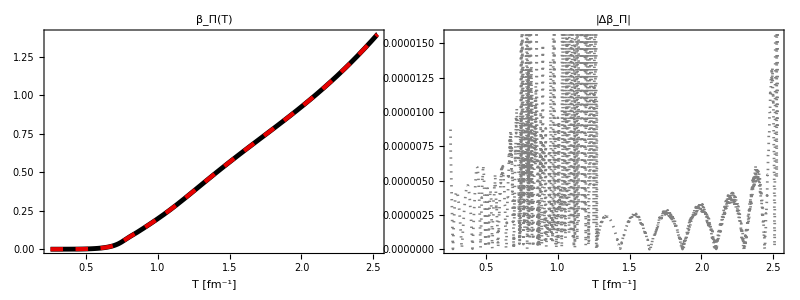

(0.20682835378500156 - 3.2867301029171436*T + 21.065833795606807*Power(T,2) - 66.78047271888437*Power(T,3) + 
     94.73374298047631*Power(T,4) + 0.043916944289792335*Power(T,5) - 112.83178964967964*Power(T,6) - 
     67.63905663285381*Power(T,7) + 180.3821078808196*Power(T,8) + 464.22133618263615*Power(T,9) - 
     610.5773302337717*Power(T,10) - 1175.6211694277858*Power(T,11) + 1945.5128702351906*Power(T,12) + 
     1347.712577455847*Power(T,13) - 5147.551329395921*Power(T,14) + 5045.699526331479*Power(T,15) - 
     2504.2064292688783*Power(T,16) + 665.8375274442221*Power(T,17) - 76.27887463424742*Power(T,18))/
   (201.98849025611145 - 1842.172522268571*T + 6803.754153600266*Power(T,2) - 12106.520664115145*Power(T,3) + 
     7218.758145890854*Power(T,4) + 9135.318235066961*Power(T,5) - 14196.767790965021*Power(T,6) - 
     6304.170479618894*Power(T,7) + 20993.51968903*Power(T,8) + 1135.396270608942*Power(T,9) - 
     28403.358089371693*Power(T,10) + 14285.703700386244*Power(T,11) + 25797.63207737443*Power(T,12) - 
     45094.484195852514*Power(T,13) + 33852.26806235173*Power(T,14) - 14959.400132356332*Power(T,15) + 
     4077.6146655020093*Power(T,16) - 632.5429421932918*Power(T,17) + 40.70510397906167*Power(T,18))

```mathematica
(* betabulk =5.0*betapi/3.0-cs2*(e+p)+cs2*mdmdT*I11 *)

Clear[betabulk,betabulkData,betabulkfit,I11DataRaw,I11Data,I11]

I11DataRaw=Import[wd<>"/betabulkplot.dat"];
I11Data= Take[I11DataRaw,{2,Length[I11DataRaw]}];
I11 = Interpolation[I11Data[[All,{1,2}]]];

betabulk[T_]=5.0/3.0*betapi[T]+cs2fit[efit[T]]*(mdmdTQuasi[T]*I11[T]-(efit[T]+Pfit[T]));

betabulkData=Table[{T,betabulk[T]},{T,Tmin,Tmax,0.001}];
betabulk=Interpolation[betabulkData];

n = 18;
betabulkfit[T_]=rationalPolyFit[betabulkData,n,n]/.{x->T};


betabulkold[T_]=(0.057187918268175174-2.5795110808844144*T+31.966143337661794*T^2-186.97202223464143*T^3+632.9739160169219*T^4-1356.8644912535221*T^5+1937.6556428262882*T^6-1901.4144609887912*T^7+1305.7115016142484*T^8-632.7107309491553*T^9+215.7883928137199*T^10-50.783337922429304*T^11+7.882963305898372*T^12-0.7302386364254765*T^13+0.031006456705249083*T^14)/(2168.5818494848654-17367.372494454743*T+62866.89323544513*T^2-136008.52657020878*T^3+196076.0893015133*T^4-198954.9682758633*T^5+146384.87731197142*T^6-79310.95783243925*T^7+31803.091369445476*T^8-9398.242646642117*T^9+2016.6245278736917*T^10-304.98512854363526*T^11+30.758339605713708*T^12-1.852389925261096*T^13+0.05027444936020055*T^14);

betabulkconformal[T_]=14.55*(1.0/3.0-cs2fit[T])^2*(efit[T]+Pfit[T]);

Grid[{{
Plot[{betabulk[T],betabulkfit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["β_Π(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betabulk[T]-betabulkfit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δβ_Π|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
(*,Plot[{betabulkfit[T]/(efit[T]+Pfit[T]),betabulkconformal[T]/(efit[T]+Pfit[T])},{T,temp[[1]],temp[[400]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]*)}}]

betabulkfit[T]//CForm
```

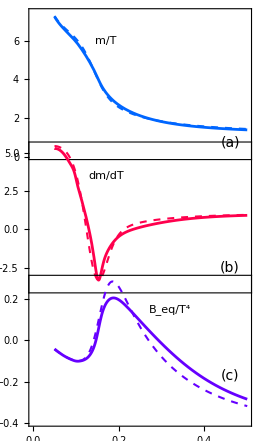
-Graphics-T (GeV)

```mathematica
legendz=Panel[Style["m/T",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendBeq=Panel[Style["B_eq/T^4",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legenddmdT=Panel[Style["dm/dT",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];

zstyle={Directive[RGBColor[0,0.4,1],AbsoluteThickness[2]],Directive[RGBColor[0,0.4,1],AbsoluteThickness[1.5],AbsoluteDashing[Small]]};
dmdTstyle={Directive[RGBColor[1,0,0.3],AbsoluteThickness[2]],Directive[RGBColor[1,0,0.3],AbsoluteThickness[1.5],AbsoluteDashing[Small]]};
Bstyle={Directive[RGBColor[0.4,0,1],AbsoluteThickness[2]],Directive[RGBColor[0.4,0,1],AbsoluteThickness[1.5],AbsoluteDashing[Small]]};

a = 25;
b= 30;

min = {0.0085,0};
maj={0.0145,0};

noTticks = {

{0.02,"",min},{0.04,"",min},{0.06,"",maj},{0.08,"",min},{0.1,"",maj},
{0.12,"",min},{0.14,"",min},{0.16,"",maj},{0.18,"",min},{0.2,"",maj},
{0.22,"",min},{0.24,"",min},{0.26,"",maj},{0.28,"",min},{0.3,"",maj},
{0.32,"",min},{0.34,"",min},{0.36,"",maj},{0.38,"",min},{0.4,"",maj},
{0.42,"",min},{0.44,"",min},{0.46,"",maj},{0.48,"",min},{0.5,"",maj}};

zplot=Plot[{zQuasifunc[T*5.067731],zold[T*5.06731]},{T,0.05,0.5},PlotRange->{{0,0.5},{0,7.5}},PlotStyle->zstyle,ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,All},{noTticks,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendz,{0.17,6}],Inset[Style["(a)",FontSize->14,FontFamily->"Calibri"],{0.46,0.75}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

dmdTplot=Plot[{mQuasifunc'[T*5.067731],mold'[T*5.067731]},{T,0.05,0.5},PlotRange->{{0,0.5},{-3.95,5.5}},PlotStyle->dmdTstyle,ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,All},{noTticks,noTticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legenddmdT,{0.17,3.5}],Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{0.46,-2.5}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

Bplot=Plot[{B0Quasifunc2[T*5.067731]/(T*5.067731)^4,Beqold[T*5.067731]/(T*5.067731)^4},{T,0.05,0.5},PlotRange->{{0,0.5},{-0.4,0.3}},PlotStyle->Bstyle,ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,All},{All,noTticks}},RotateLabel->False,BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendBeq,{0.32,0.15}],Inset[Style["(c)",FontSize->14,FontFamily->"Calibri"],{0.46,-0.17}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

quasi=Panel[GraphicsGrid[{{zplot},{dmdTplot},{Bplot}},Spacings->{0,-44.2}],Style["T (GeV)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Background->White,ImageSize->{280,456}]

Export["quasi.pdf",quasi];
```

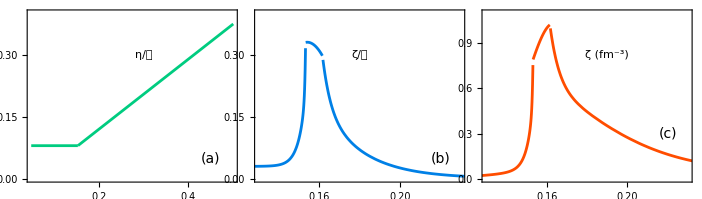
-Graphics-T (GeV)

```mathematica
legendηs=Panel[Style["η/𝒮",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendζs=Panel[Style["ζ/𝒮",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendζ=Panel[Style["ζ (fm^-3)",FontSize->18,FontFamily->"Calibri"],Background->White,FrameMargins->0];

Tc = 0.154;
ηsmin = 0.08;
ηsslope =0.85;

ζsnorm = 1.25;
a0=-13.45;
a1=27.55;
a2=-13.77;
lambda1=0.9;
lambda2=0.25;
lambda3=0.9;
lambda4=0.22;
sigma1=0.025;
sigma2=0.13;
sigma3=0.0025;
sigma4=0.022;


ηsfunc[T_]=Piecewise[{

{ηsmin,T<Tc},
{ηsmin+ηsslope*(T-Tc),T≥Tc}
}];

ζsfunc[x_]=Piecewise[{
(* x = T/Tc*)
{lambda3*Exp[(x-1.0)/sigma3]+lambda4*Exp[(x-1.0)/sigma4]+0.03,x<0.995},
{(a0+a1*x+a2*x*x),0.995<x<1.05},
{lambda1*Exp[-(x-1.0)/sigma1]+lambda2*Exp[-(x-1.0)/sigma2]+0.001,x>1.05}
}];



etas =Plot[ηsfunc[T],{T,0.05,0.5},PlotRange->{{0.05,0.5},{0,0.4}},PlotStyle->Directive[RGBColor[0.0,0.8,0.5],AbsoluteThickness[2]],ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{All,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendηs,{0.3,0.3}],Inset[Style["(a)",FontSize->14,FontFamily->"Calibri"],{0.45,0.05}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

zetas =Plot[ζsfunc[T/Tc],{T,0.05,0.5},PlotRange->{{0.13,0.23},{0,0.4}},PlotStyle->Directive[RGBColor[0.0,0.5,0.9],AbsoluteThickness[2]],ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{All,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendζs,{0.18,0.3}],Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{0.22,0.05}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

zeta =Plot[ζsfunc[T/Tc]*Sfit[T*5.067731],{T,0.05,0.5},PlotRange->{{0.13,0.23},{0,1.1}},PlotStyle->Directive[RGBColor[1.0,0.3,0],AbsoluteThickness[2]],ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{All,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendζ,{0.19,0.82}],Inset[Style["(c)",FontSize->14,FontFamily->"Calibri"],{0.22,0.3}]},ImagePadding->{{a,b},{Automatic,Automatic}}];


viscosity=Panel[GraphicsGrid[{{etas,zetas,zeta}},Spacings->{-20,0}],Style["T (GeV)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Background->White,ImageSize->{700,210}]

Export["viscosity.pdf",viscosity];
```

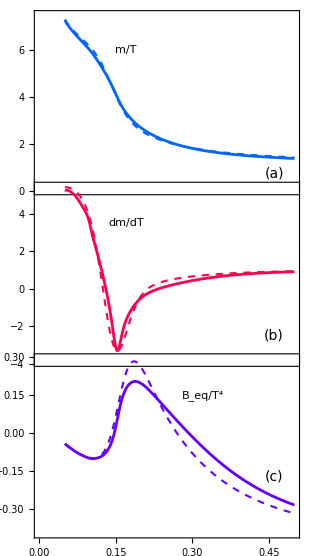
-Graphics-T (GeV)

```mathematica
zplot=Plot[{zQuasifunc[T*5.067731],zold[T*5.06731]},{T,0.05,0.5},PlotRange->{{0,0.5},{0,7.5}},PlotStyle->zstyle,ImageSize->300,Frame->True,Axes->False,FrameTicks->{{All,All},{noTticks,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendz,{0.17,6}],Inset[Style["(a)",FontSize->14,FontFamily->"Calibri"],{0.46,0.75}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

dmdTplot=Plot[{mQuasifunc'[T*5.067731],mold'[T*5.067731]},{T,0.05,0.5},PlotRange->{{0,0.5},{-3.95,5.5}},PlotStyle->dmdTstyle,ImageSize->300,Frame->True,Axes->False,FrameTicks->{{All,All},{noTticks,noTticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legenddmdT,{0.17,3.5}],Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{0.46,-2.5}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

Bplot=Plot[{B0Quasifunc2[T*5.067731]/(T*5.067731)^4,Beqold[T*5.067731]/(T*5.067731)^4},{T,0.05,0.5},PlotRange->{{0,0.5},{-0.4,0.3}},PlotStyle->Bstyle,ImageSize->300,Frame->True,Axes->False,FrameTicks->{{All,All},{All,noTticks}},RotateLabel->False,BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendBeq,{0.32,0.15}],Inset[Style["(c)",FontSize->14,FontFamily->"Calibri"],{0.46,-0.17}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

quasi=Panel[GraphicsGrid[{{zplot},{dmdTplot},{Bplot}},Spacings->{0,-43.6}],Style["T (GeV)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Background->White,ImageSize->{327,570}]

Export["quasi_big.pdf",quasi];
```